```mathematica
Ham=A/2{{7/4,2^(1/2)},{2^(1/2),11/4}}-μe B {{-1/2,0},{0,1/2}}-μn B{{1,0},{0,0}}
```

{{(7 A)/8+(B μe)/2-B μn,A/(√2)},{A/(√2),(11 A)/8-(B μe)/2}}

```mathematica
Eigensystem[Ham]
```

{{1/8 (9 A-4 B μn-2 √(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),1/8 (9 A-4 B μn+2 √(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2))},{{-(A-2 B μe+2 B μn+√(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2))/(2 √2 A),1},{-(A-2 B μe+2 B μn-√(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2))/(2 √2 A),1}}}

```mathematica
Ham1=A/2{{11/4,2^(1/2)},{2^(1/2),7/4}}-μe B {{-1/2,0},{0,1/2}}-μn B{{0,0},{0,-1}}
```

{{(11 A)/8+(B μe)/2,A/(√2)},{A/(√2),(7 A)/8-(B μe)/2+B μn}}

```mathematica
Eigensystem[Ham1]
```

{{1/8 (9 A+4 B μn-2 √(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),1/8 (9 A+4 B μn+2 √(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2))},{{(A+2 B μe-2 B μn-√(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2))/(2 √2 A),1},{(A+2 B μe-2 B μn+√(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2))/(2 √2 A),1}}}

```mathematica
cond={A->228/1.5,μe->1.4,μn->0.001}
```

{A→152.,μe→1.4,μn→0.001}

```mathematica
spec={A/8*15-μe B /2-μn B,1/8 (9 A-4 B μn-2 √(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),1/8 (9 A-4 B μn+2 √(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),1/8 (9 A+4 B μn-2 √(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),1/8 (9 A+4 B μn+2 √(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),
A/8*15+μe B /2+μn B}-A 3/8
```

{(3 A)/2-(B μe)/2-B μn,-(3 A)/8+1/8 (9 A-4 B μn-2 √(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),-(3 A)/8+1/8 (9 A-4 B μn+2 √(9 A^2-4 A B μe+4 B^2 μe^2+4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),-(3 A)/8+1/8 (9 A+4 B μn-2 √(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),-(3 A)/8+1/8 (9 A+4 B μn+2 √(9 A^2+4 A B μe+4 B^2 μe^2-4 A B μn-8 B^2 μe μn+4 B^2 μn^2)),(3 A)/2+(B μe)/2+B μn}

```mathematica
graph=Plot[spec/.cond,{B,0,1000},AxesLabel->{"B(G)","E/μ_Bh(MHz)"},LabelStyle->Directive[Bold,Larger], Ticks->{{0,200,400,600,800,1000},{-600,-400,-200,0,200,400,600,800}},AxesStyle->Arrowheads[Automatic]]
```

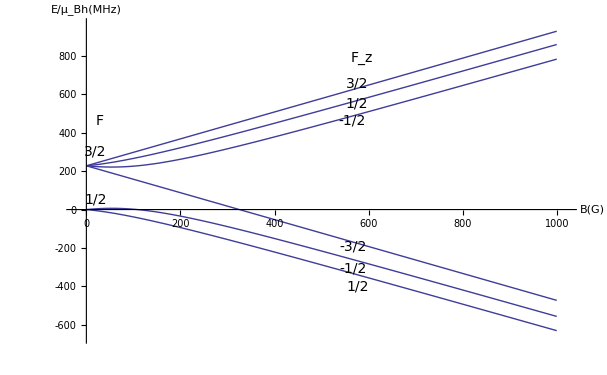
```mathematica
newGraph=-Graphics-
```

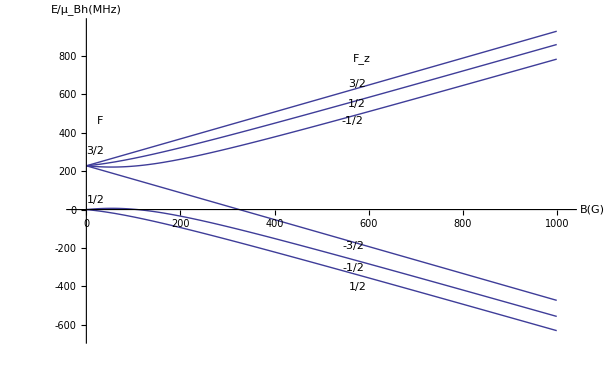

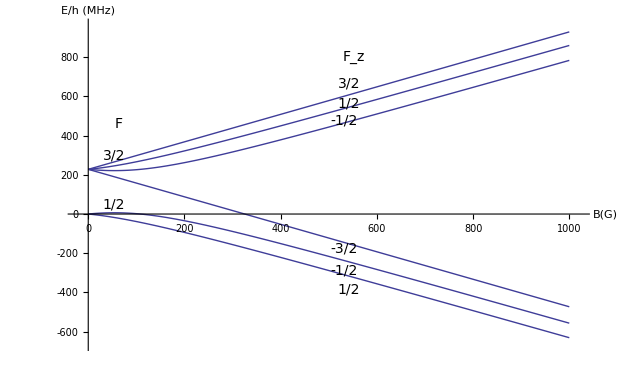
```mathematica
newGraph=-Graphics-
```

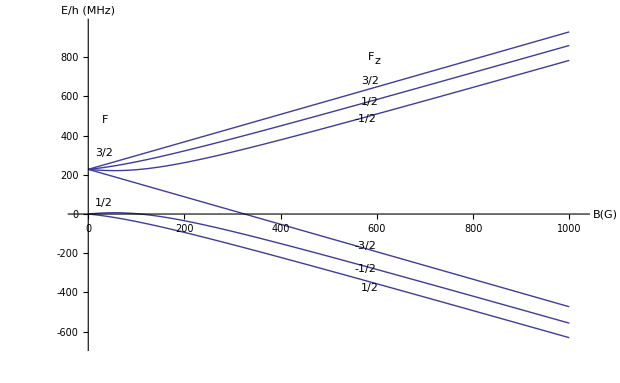

```mathematica
Text[Zeeman Energy E/h (Mhz)]
```

(ⅇ Energy Mhz Zeeman)/h

```mathematica
label=-Graphics-;
```

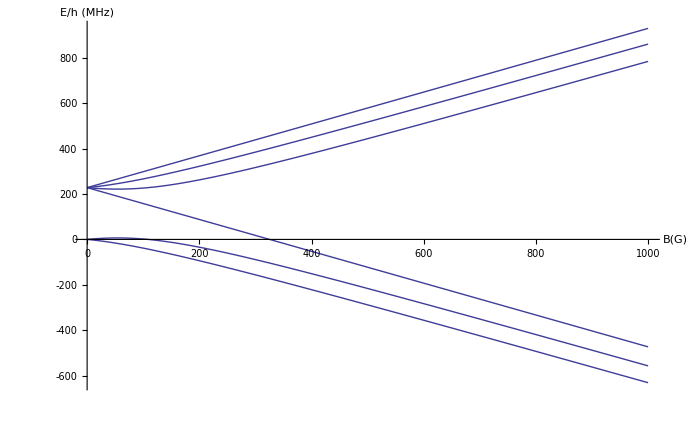

-Graphics-

```mathematica
Show[graph]
```

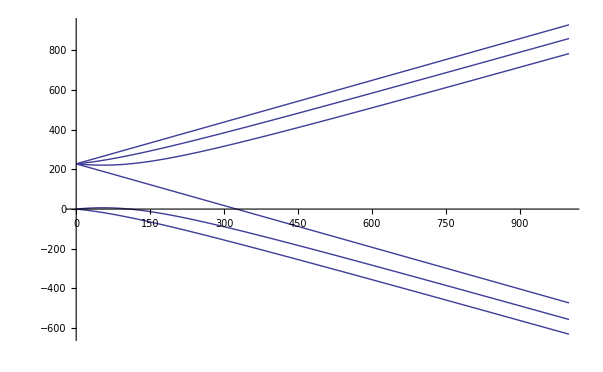

```mathematica
Plot[spec/.cond,{B,0,1000},AxesStyle->Arrowheads[Automatic]]
```